```mathematica
L = 1
```

1

```mathematica
psi[x_, n_] := Sqrt[2/L] Sin[Pi/L  x n]
```

```mathematica
psis[x_, n_] := Sum[psi[x, i]^2, {i, 1, n/2}]
```

```mathematica
plot[n_] := Plot[psis[x, n], {x, 0, L}, PlotRange -> Full]
```

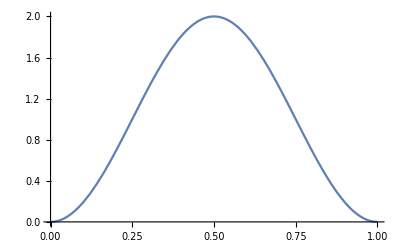

```mathematica
plot[2]
```

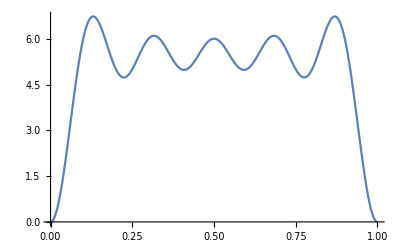

```mathematica
plot[10]
```

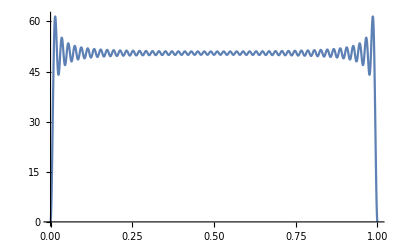

```mathematica
plot[100]
```